```mathematica
tabb=Table[{z,x/.NSolve[x==x^(3 z),x,Reals][[1]]},{z,0,10,1}]
```

{{0,1.},{1,-1.},{2,0},{3,-1.},{4,0},{5,-1.},{6,0},{7,-1.},{8,0},{9,-1.},{10,0}}

```mathematica
f=Interpolation[tabb]
```

InterpolatingFunction[…]

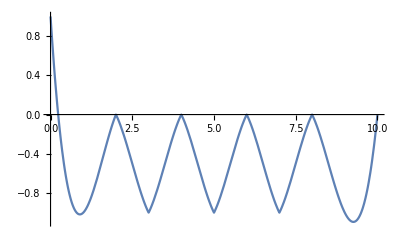

```mathematica
Plot[f[z],{z,0,10}]
```

```mathematica
Manipulate[Plot[{x,Tanh[h x]},{x,0,1}],{h,1,10}]
```